{-0.0255472,-0.0170832,-0.0163553,-0.0134707,-0.0128886,-0.0130445,-0.00998382,-0.0213525,-0.0246125,-0.0197272,-0.0180869,-0.019894,-0.0185458}

137.344

32.7288

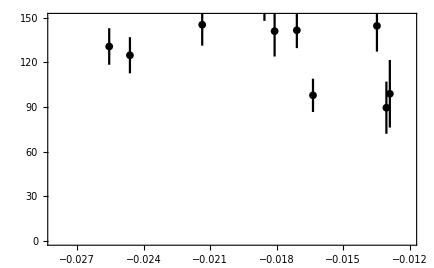

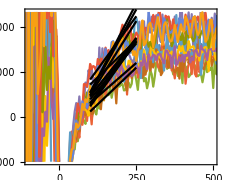

```mathematica
cm=72/2.54;
dtt=Import["C:\\Users\\cs2002\\00_WORK\\00_Chris\\2019\\190607_TRM_TAM_WSe2_PC\\07062019\\output\\PC_790_power_single_sigma_DTT_values.dat","Table"][[1]];
dtt=Take[dtt,{1,13}]

trans=Import["C:\\Users\\cs2002\\00_WORK\\00_Chris\\2019\\190607_TRM_TAM_WSe2_PC\\07062019\\output\\PC_790_power_single_sigma_shifted.dat","Table"];

time=Table[(i-30)*5,{i,0,139}];

transnew=Table[Transpose[{time,trans[[i]]}],{i,1,13}];

dyn=ListLinePlot[transnew, Frame->True,FrameStyle->Black,FrameTicks->{{True,False},{True,False}}, PlotRange->{{-200,500},{150,200}},
PlotStyle->{AbsoluteThickness[1]},
Axes->False,
AspectRatio->0.8,
ImageSize->8cm];

msd=Table[Transpose[{time,trans[[i]]^2 - (trans[[i]][[45]])^2}],{i,1,13}];

pmsd=ListLinePlot[msd, Frame->True,FrameStyle->Black,FrameTicks->{{True,False},{True,False}}, PlotRange->{{-100,500},{-3000,7000}},
Axes->False,
AspectRatio->0.8,
ImageSize->8cm];


fitdata=msd[[1]];

d1=Table[Take[msd[[i]],{45,70}],{i,1,13}];

lm1=Table[LinearModelFit[d1[[i]],x,x],{i,1,13}];
Table[lm1[[i]]["ParameterTable"],{i,1,13}];

vals=Table[lm1[[i]]["ParameterTableEntries"],{i,1,13}];

diffusion=Table[vals[[i]][[2]]*10/2,{i,1,13}];


diffusionVAL=Table[diffusion[[i]][[1]],{i,1,13}];
Mean[diffusionVAL]
StandardDeviation[diffusionVAL]


diffusionSTD=Table[diffusion[[i]][[2]],{i,1,13}];

Needs["ErrorBarPlots`"]
perr=ErrorListPlot[Table[{{dtt[[i]],diffusionVAL[[i]]},ErrorBar[diffusionSTD[[i]]]},{i,1,13}],PlotStyle->Black,PlotRange->{{-0.028,-0.012},{0,150}},Frame->True]

fullmsd=Show[pmsd,Table[Plot[lm1[[i]][x],{x,100,250},PlotStyle->Black],{i,1,13}]]
```

```mathematica
Export["C:\\Users\\cs2002\\00_WORK\\00_Chris\\2019\\190607_TRM_TAM_WSe2_PC\\07062019\\output\\PC_790_power_single_sigma_shifted.svg",perr]
```

C:\Users\cs2002\00_WORK\00_Chris\2019\190607_TRM_TAM_WSe2_PC\07062019\output\PC_790_power_single_sigma_shifted.svg